## Constants

```mathematica
"It looks like (from below) that the input needed for the screening code is the αs and βs which are functions of the number densities computed here. So I think all we need to do is compute the free number densities as function of input mass and then we good."
```

It looks like (from below) that the input needed for the screening code is the αs and βs which are functions of the number densities computed here. So I think all we need to do is compute the free number densities as function of input mass and then we good.

```mathematica
(*make sure to run appendix_benchmark_values.nb first*)
```

```mathematica
me=5.11*10^5; (*eV*)
α=1/137;
REarth = 32.322 *10^12; (*eV^-1*)
nF(*[mX_]*):= 2.3*10^(-17)(*0.1*3841/mX*); (*eV^3*)
T= 119(*2.643*); (*eV*)
MEarth = 3.35041*10^(60); (*eV*)
G = 6.70883*10^(-57);(*eV^-2*)
TEarth = 0.345; (*eV - this is in the core*)
(*Particle masses from David's code, in eV*)
mMeeV= currentfoverv*511/1000*10^-3*10^(9);
mHeV = mHGeV[currentfoverv]*10^(9);
mHeeV=4*mHGeV[currentfoverv]*10^(9); 

QX= 2; (*change this to adjust charge of DM*)

(*Free particle densities from David's code, in natural units*)
nFHeeV=currentY (3/10)/(mHeeV*10^(-9))*5/100*7.68*10^(-15);
nFMeeV=currentY (3/10)/(mHeeV*10^(-9))*(5*2)/100*7.68*10^(-15);

(*velocity characteristics of free DM, all in natural units*)
v0HeeVD=SetPrecision[v0kmsHeDisk[currentfoverv,currentY]*(*(30)**)10^5*3.33*10^(-11),20];(*v0 for He in galactic system frame, but not earth frame*)
v0EeVD=SetPrecision[v0kmsEDisk[currentfoverv,currentY]*(*(30)**)10^5*3.33*10^(-11),20];  (*v0 for E in galactic system frame, but not earth frame*)

v0HeeVH=SetPrecision[v0kmsHeHalo[currentfoverv,currentY]*(*(30)**)10^5*3.33*10^(-11),20];(*v0 for He in galactic system frame, but not earth frame*)
v0EeVH=v0kmsEHalo[SetPrecision[currentfoverv,currentY]*(*(30)**)10^5*3.33*10^(-11),20];  (*v0 for E in galactic system frame, but not earth frame*)

(*velocity distributions calculated in David's code*)
fHeDisk[v_]:=(correctf[v/(10^5*3.33*10^(-11))]/.{vescape->vescapehuge, ve->vEarthkmsDisk, v0->v0kmsHeDisk[currentfoverv,currentY]})/(10^5*3.33*10^(-11)); 
fHeHalo[v_]:=(correctf[v/(3.33*10^(-6))]/.{vescape->vescapehuge, ve->vEarthkmsHalo, v0->v0kmsHeHalo[currentfoverv,currentY]})/3.33*10^(-6);
MBNorm[v0_]:=SetPrecision[NIntegrate[v^2 Exp[-3/2 v^2/v0^2],{v,0,10v0}],20];
fH[v_,v0_]:=SetPrecision[ Sqrt[v^2+v2esc[0,5*10^9]]*v^2 Exp[-3/2 v^2/v0^2]/MBNorm[v0],20];
```

InterpolatingFunction::dmval: Input value {9.99×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

## Make Target List

```mathematica
(*Note on conventions: all atoms named by normal abbr. OR if abbr. is 1 letter, by first 2 letters of atom name*)
(*find number density in (eV)^-3 from mass fraction, mass in amu's*)
findnT[massfrac_,amass_]:=massfrac/amass*(5.97217*10^(24))/(1.66054*10^(-27))/(1.4145*10^(41)); 
(*find mass of atom in eV*)
findmT[amass_]:=amass*9.314*10^(8);

(* {Z, massfrac in Earth, mass in amu, number density, mass in eV}*)
OX = {8,.297,15.999,findnT[.297,15.999],findmT[15.999]};
MG = {12,.154,24.305,findnT[.154,24.305],findmT[24.305]};
SI= {14,.161,28.085,findnT[.161,28.085],findmT[28.085]};
FE={26,.319,55.845,findnT[.319,55.845],findmT[55.845]};
AL = {13,.0159,26.982,findnT[.0159,26.982],findmT[26.982]};
CA = {20,.0171,40.078,findnT[.0171,40.078],findmT[40.078]};
NI = {28,.0182,58.693,findnT[.0182,58.693],findmT[58.693]};
HY = {1,.00026,1.008,findnT[.00026,1.008],findmT[1.008]};
SU= {16,.00635,32.06,findnT[.00635,32.06],findmT[32.06]};
CR = {24,.0047,51.996,findnT[.0047,51.996],findmT[51.996]};
NA = {11,.0018,22.990,findnT[.0018,22.990],findmT[22.990]};
CA= {6,.00073,12.011,findnT[.00073,12.011],findmT[12.011]};
PH = {15,.00121,30.974,findnT[.00121,30.974],findmT[30.974]};
```

```mathematica
targList = {OX,MG,SI,FE,AL,CA,NI,HY,SU,CR,NA,CA,PH};
```

## Charge Shielding (Disk)

```mathematica
alphaH = 0;
alphaHe = 2*nFHeeV/(4*nFHeeV+nFMeeV);
alphaE = -nFMeeV/(4*nFHeeV+nFMeeV);
beta0 = 10*10^23/(4*Pi*REarth^3/3)/(4*nFHeeV+nFMeeV);
"where does this 10^24come from?"
phiEarth = 0.05 (*set the potential at the Earth's surface*)
```

where does this 10^24come from?

0.05

#### Constants - only essentials

```mathematica
alphaH = 0;
alphaHe = 1/3;
alphaE = -1/3;
beta0 = 0.04857165133287997;
"where does this 10^24come from?"
phiEarth = 0.05
```

where does this 10^24come from?

0.05

```mathematica
me=5.11*10^5; (*eV*)
α=1/137;
REarth = 32.322 *10^12; (*eV^-1*)
nF(*[mX_]*):= 2.3*10^(-17)(*0.1*3841/mX*); (*eV^3*)
T= 119(*2.643*); (*eV*)
MEarth = 3.35041*10^(60); (*eV*)
G = 6.70883*10^(-57);(*eV^-2*)
TEarth = 0.345; (*eV - this is in the core*)
```

#### Numeric

```mathematica
(*numeric calculation of screening in delta function case from MDM paper*)
```

```mathematica
vrat = 1; (*adjust the velocity at infinity, vrat = (2/3 v0^2)/Subscript[v, ∞]^2*)
```

```mathematica
smallrETerm[RMax_,r_,phi_,phiRMax_]:=Piecewise[{{0,r>RMax},{Re[Sqrt[1+phi]Sqrt[1+phi-RMax^2/r^2(1+phiRMax)]],r<=RMax}}];
```

```mathematica
rList=Table[1- 10^-5 i,{i,2000}];
rhoConstVList={};
indexConstV=1;
rhoEarth=beta0/(2*alphaH+3*alphaHe);
While[True,root=phi/.FindRoot[alphaHe*(1-2 *vrat*phi)+alphaE*(1+ vrat*phi-smallrETerm[1,rList[[indexConstV]], vrat*phi,0]),{phi,0.00001,rhoEarth},Method->"Brent"];
 If[root>=rhoEarth-10^(-4),Break[]];AppendTo[rhoConstVList,{rList[[indexConstV]],root}];indexConstV++]
```

```mathematica
(*RMax initially set to 1, rescale to match REarth*)
rescaleRMaxVConst[elem_]:={elem[[1]]/rhoConstVList[[-1,1]],elem[[2]]};
rescaledrhoConstVList=rescaleRMaxVConst/@rhoConstVList;
```

```mathematica
numericalConstV=ListPlot[rescaledrhoConstVList];
```

```mathematica
numericalConstVURS = ListPlot[rhoConstVList] (*not rescaled*);
```

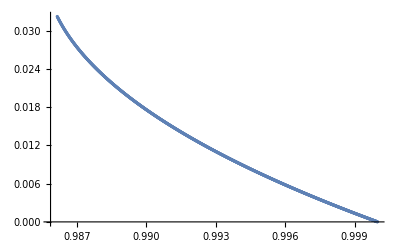

```mathematica
rescaleVURS[elem_]:={elem[[1]],2*elem[[2]]/3};
numericalConstVURSR=ListPlot[Map[rescaleVURS,rhoConstVList]]
```

#### MB Distribution Case

```mathematica
N@vInfList 
"What are the units here?"
```

{0.05,0.06,0.072,0.0864,0.10368,0.124416,0.149299,0.179159,0.214991,0.257989,0.309587,0.371504,0.445805,0.534966,0.641959,0.770351,0.924421,1.10931,1.33117,1.5974,1.91688,2.30026,2.76031,3.31237,3.97484}

What are the units here?

```mathematica
(*create lists for recursion over vinf to find RMax(vinf), also define MB distribution weight factor to match velocities in vInfList*)
vInfList=PowerRange[1/20,4,1+2/10];
MBfactor[i_]:=SetPrecision[ vInfList[[i]]^2 Exp[-3/2 vInfList[[i]]^2]/MBNorm,20];
MBNorm=SetPrecision[Sum[vInfList[[i]]^2 Exp[-3/2 vInfList[[i]]^2],{i,1,Length[vInfList]}],20];
(*helper functions for the recursion below. *)
```

```mathematica
derivF[i_,RMax_,r_,phi_?NumericQ,n_]:=
(*Used to find a good endpoint for solving the F[phi]=0 equation (there can be a superfluous root at higher phi)*)Re[N[(-3 ⅇ^(-3phi)/2-3 ⅇ^(3phi/2)/2)/n+((MBfactor[i]/(2*√(vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]]))vInfList[[i]]))),20]];(*CHANGED*)

complexF[i_,RMax_,r_]:=
(*find where the function F[phi] (where we are solving F[phi]=0 to find phi) goes complex, which will cause the root finding protocol to not work well*)
N[RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]])-vInfList[[i]]^2,50];

rootF[i_,RMax_,r_,phi_?NumericQ,n_]:=

Re[N[(ⅇ^(-3phi/2)-ⅇ^(3phi/2))/n+MBfactor[i]/vInfList[[i]] Sqrt[vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]])],50]];(*CHANGED*)
```

```mathematica
(* start of recursion to scan over different r's to find escape potential *)
phiList={{1,0}};
RMaxList={{1,0}};
minPoint =SetPrecision[ 0.5,20];(*CHANGED*)
pointNumber=100(*keep this number low for fast run times, ~100 works well*);(*CHANGED*)
Clear[scanPoints];
scanPoints=SetPrecision[Table[1-i(1-minPoint)/pointNumber,{i,pointNumber}],20];
earthFlag=False (*triggers True when escape potential matches Earth potential*);
zoomFlag=False (*triggers True when the recursion zooms in to finer value of the radius*);
(*recursion over different values of v_inf*)
Do[
phiListWorking = {};
delNum=0;
zoomCount=0;
If[earthFlag,Break[]];
If[zoomFlag,Break[]];
Print[j];
(*recursion over different values of r*);
Do[
If[zoomCount>12,zoomFlag=True;Print["You've zoomed in more than 12 times, problem?"];
Break[]];

phiMin=Max[Table[complexF[l,RMaxList[[l,1]],scanPoints[[k]]],{l,j}]]+10^(-15);
Do[If[Sqrt[vInfList[[l]]^2+phiMin-RMaxList[[l,1]]^2/scanPoints[[k]]^2(vInfList[[l]]^2+RMaxList[[l,2]])]<=10^-8,
phiMin+=10^-12],
{l,j}];

phiMax=phi/.FindRoot[Sum[derivF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j],{i,1,j}],{phi,phiMin,0.1},Method->"Brent"];

res=Check[FindRoot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j],{i,1,j}],
{phi,phiMin-10^(-12),phiMax},
Method->"Brent",WorkingPrecision->20],$Failed[Evaluate@$MessageList],
FindRoot::bbrac];


If[
FreeQ[res,$Failed](*check whether FindRoot was succesful*),
successplot=Plot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j],{i,1,j}],{phi,phiMin-10^(-12),phiMax}];(*ADDED*)
phiNew=phi/.res;
If[phiNew>phiEarth,(*CHANGED*)
earthFlag=True;phiList=Join[phiList,phiListWorking];Print["Reached Earth phi"];
Break[]];

(*make updated potential function so far*);
AppendTo[phiListWorking,{scanPoints[[k]],phiNew}];
phiFunc=Interpolation[Join[phiList,phiListWorking]];
delNum+=1;

(*check if we have hit RMax(v_inf)*);
If[phiFunc'[scanPoints[[k]]]*scanPoints[[k]]+2phiFunc[scanPoints[[k]]]+2(vInfList[[j+1]])^2<=0,AppendTo[RMaxList,{scanPoints[[k]],phiNew}];
phiList=Join[phiList,phiListWorking];
scanPoints=Drop[scanPoints,delNum];
pointNumber-=k;
Return[phiList[[-1]]];];,

(*if FindRoot was not succesful, go back a step in r and insert extra points to "fine-grain" your scan over r*)
Print["Zooming In"];
ckplot=Plot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j],{i,1,j}],{phi,phiMin-10^(-12),phiMax}];(*ADDED*)
zoomCount+=1;
(*pick extra points to insert*);
If[k==1,insertPoints=Table[RMaxList[[j,1]]-(RMaxList[[j,1]]-scanPoints[[k]])/10 p,{p,0,9}],insertPoints=Table[scanPoints[[k-1]]+(scanPoints[[k]]-scanPoints[[k-1]])/10 p,{p,0,9}]];

scanPoints=Join[scanPoints[[1;;k-1]],insertPoints,scanPoints[[k;;]]];
pointNumber+=10;
delNum+=1
],

{k,10000}],
{j,1,Length[vInfList]-1}];
```

1

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

Zooming In

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

2

3

4

5

6

7

8

9

10

11

12

13

Reached Earth phi

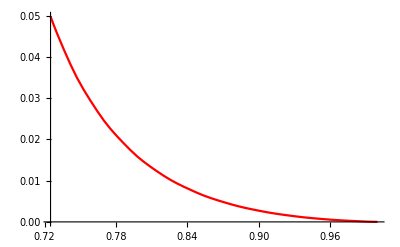

```mathematica
f=Interpolation[phiList];
testCurrent=Plot[f[x],{x,phiList[[-1,1]],1}(*,PlotRange->{{.99903634,1},{0,.011}}*),PlotStyle->Red]
```